```mathematica
testFileName = "/Users/chengling/Downloads/bd_N1024_p3.75000_T0.00055000_t100000.000000_10.nc";
```

```mathematica
filename = StringJoin["/Users/chengling/Downloads/nvt_N1024_p3.75000_T0.15000000_t100000.000000_",ToString[],".nc"]
```

ToString::argt: ToString called with 0 arguments; 1 or 2 arguments are expected.

StringJoin::string: String expected at position 2 in /Users/chengling/Downloads/nvt_N1024_p3.75000_T0.15000000_t100000.000000_<>ToString[]<>.nc.

/Users/chengling/Downloads/nvt_N1024_p3.75000_T0.15000000_t100000.000000_<>ToString[]<>.nc

```mathematica
readFile[foretxt_,index_]:=Module[{position,velocity,type,additionalData,boxMatrix,time},
{position,velocity,type,additionalData,boxMatrix,time}=Import[StringJoin[foretxt,ToString[index],".nc"],"Data"];
{position,boxMatrix}]
```

```mathematica
time-10000
```

{{1.57852×10^-6},{0.00200158},{0.00300158},{0.00400158},{0.00600158},{0.0100016},{0.0160016},{0.0250016},{0.0400016},{0.0630016},{0.100002},{0.158002},{0.251002},{0.398002},{0.631002},{1.},{1.585},{2.512},{3.981},{6.31},{10.},{15.849},{25.119},{39.811},{63.096},{100.},{158.489},{251.189},{398.107},{630.957},{1000.},{1584.89},{2511.89},{3981.07},{6309.57},{10000.},{15848.9},{25118.9},{39810.7},{63095.7}}

```mathematica
{position,velocity,type,additionalData,boxMatrix,time}=Import["/Users/chengling/Downloads/nvt_N1024_p3.75000_T0.15000000_t100000.000000_0.nc","Data"];
```

```mathematica
DIM=2;
boxInvTrans[boxmat_,pt_]:=Module[{invmat},
invmat=Inverse[boxmat];
invmat.pt
];
boxTrans[boxmat_,pt_]:=boxmat.pt;
putInBox[boxmat_,pt_]:=Module[{temp},
temp=boxInvTrans[boxmat,pt];
Do[
If[Between[temp[[dd]]==False,{0,1}],temp[[dd]]-=Sign[temp[[dd]]]];
,{dd,1,DIM}];
boxTrans[boxmat,temp]
];
minDist[boxmat_,ptA_,ptB_]:=Module[{vA,vB,disp},
vA=boxInvTrans[boxmat,ptA];
vB=boxInvTrans[boxmat,ptB];
disp=vA-vB;
Do[
If[Abs[disp[[dd]]]>0.5,disp[[dd]]-=Sign[disp[[dd]]]];
,{dd,1,DIM}];
boxTrans[boxmat,disp]
];
```

```mathematica
overlapFunction[d_]:=If[d>0.5,0,1]
computeOverlap[inipts_,pts_,boxmat_]:=Module[{minDists,minLenths,overlaps},
minDists=Table[minDist[boxmat,inipts[[i]],pts[[i]]],{i,1,Length[pts]}];
minLenths=Table[Sqrt[minDists[[i,1]]^2+minDists[[i,1]]^2],{i,1,Length[pts]}];
overlaps= Table[overlapFunction[minLenths[[i]]],{i,1,Length[pts]}];
Total[overlaps]/Length[pts]
]
```

```mathematica
N[computeOverlap[Partition[position[[1]],2],Partition[position[[20]],2],Partition[boxMatrix[[1]],2]]]
```

```mathematica
xlist=Table[(i-1)/5-2,{i,1,Length[position]}]
```

{-2,-9/5,-8/5,-7/5,-6/5,-1,-4/5,-3/5,-2/5,-1/5,0,1/5,2/5,3/5,4/5,1,6/5,7/5,8/5,9/5,2,11/5,12/5,13/5,14/5,3,16/5,17/5,18/5,19/5,4,21/5,22/5,23/5,24/5,5,26/5,27/5,28/5,29/5}

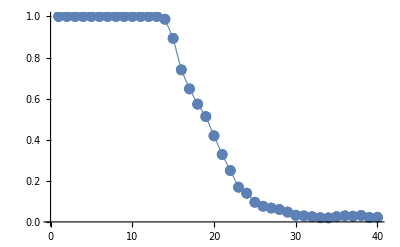

```mathematica
ListLinePlot[Table[N[computeOverlap[Partition[position[[1]],2],Partition[position[[i]],2],Partition[boxMatrix[[i]],2]]],{i,1,Length[position]}],PlotStyle->Thickness[0.002],Mesh->Full]
```

```mathematica
T015nh=Table[{position,boxMatrix}=readFile["/Users/chengling/Downloads/nvt_N1024_p3.75000_T0.15000000_t100000.000000_",j];
Table[N[computeOverlap[Partition[position[[1]],2],Partition[position[[i]],2],Partition[boxMatrix[[i]],2]]],{i,1,Length[position]}],{j,1,8}]
```

```mathematica
T00055nh=Table[{position,boxMatrix}=readFile["/Users/chengling/Downloads/nvt_N1024_p3.75000_T0.00055000_t100000.000000_",j];
Table[N[computeOverlap[Partition[position[[1]],2],Partition[position[[i]],2],Partition[boxMatrix[[i]],2]]],{i,1,Length[position]}],{j,1,5}]
```

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
T015mean= Mean/@Transpose[T015]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999756,0.983032,0.887573,0.73584,0.643188,0.591919,0.483643,0.394409,0.316284,0.251587,0.193115,0.162231,0.124512,0.0942383,0.0742188,0.0565186,0.0426025,0.03479,0.0302734,0.0249023,0.0212402,0.0227051,0.0249023,0.0222168,0.0228271,0.0255127,0.0220947,0.0212402}

```mathematica
T00055mean= Mean/@Transpose[T00055]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999609,0.958203,0.932422,0.721484,0.872461}

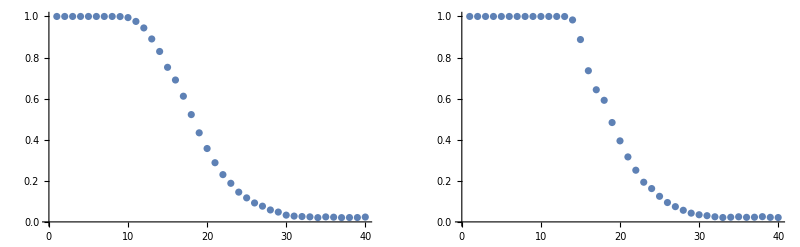

```mathematica
plot1=ListPlot[Mean/@Transpose[T015bd]];
plot2=ListPlot[Mean/@Transpose[T015nh]];
GraphicsRow[{plot1,plot2}]
```

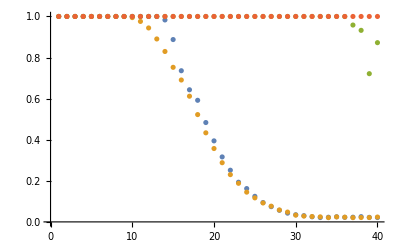

```mathematica
plot2=ListPlot[{Mean/@Transpose[T015nh],Mean/@Transpose[T015bd],Mean/@Transpose[T00055bd],Mean/@Transpose[T00055nh]}]
```

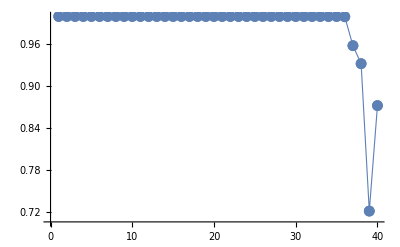

```mathematica
ListLinePlot[T00055mean,PlotStyle->Thickness[0.002],Mesh->Full]
```

```mathematica
paperHighT={-0.9983361064891847,0.9961389961389959,
-0.9251247920133111,0.9903474903474901,
-0.8452579034941763,0.9826254826254824,
-0.7587354409317802,0.969111969111969,
-0.6855241264559068,0.9517374517374515,
-0.6256239600665556,0.9362934362934361,
-0.5657237936772046,0.9150579150579148,
-0.5124792013311148,0.8938223938223936,
-0.465890183028286,0.8745173745173743,
-0.41930116472545764,0.8532818532818531,
-0.3594009983361064,0.826254826254826,
-0.3061564059900166,0.8030888030888028,
-0.26622296173044946,0.7779922779922778,
-0.22628951747088188,0.7548262548262545,
-0.17970049916805308,0.7277992277992276,
-0.13976705490848573,0.7027027027027025,
-0.09983361064891838,0.6756756756756754,
-0.05990016638935103,0.6525096525096523,
-0.0266222961730449,0.6312741312741311,
0.006655574043261225,0.6119691119691117,
0.039933444259567574,0.5907335907335906,
0.07321131447587348,0.5694980694980694,
0.10648918469217983,0.5463320463320461,
0.13976705490848573,0.5250965250965249,
0.17970049916805308,0.4999999999999998,
0.22628951747088188,0.4729729729729727,
0.259567387687188,0.4498069498069496,
0.29284525790349414,0.4285714285714284,
0.3327787021630615,0.4034749034749032,
0.36605657237936784,0.38223938223938203,
0.39933444259567374,0.36100386100386084,
0.4392678868552413,0.3359073359073357,
0.4925124792013311,0.3088803088803087,
0.5324459234608985,0.2876447876447875,
0.579034941763727,0.26833976833976814,
0.6189683860232944,0.24903474903474887,
0.6722129783693842,0.22393822393822382,
0.7254575707154745,0.20463320463320445,
0.7787021630615643,0.18146718146718133,
0.8319467554076536,0.16409266409266388,
0.8985024958402663,0.14285714285714268,
0.9717138103161398,0.12162162162162149,
1.0316139767054908,0.10617760617760608,
1.1114808652246255,0.09073359073359066,
1.1913477537437602,0.07335907335907321,
1.2845257903494174,0.06177606177606165,
1.377703826955075,0.05212355212355213,
1.4775374376039934,0.04054054054054035,
1.6239600665557403,0.02895752895752879,
1.7437603993344424,0.02316602316602312,
1.8435940099833608,0.01737451737451723,
1.9434276206322796,0.013513513513513375,
2.0166389351081526,0.01158301158301156,
2.0831946755407653,0.01158301158301156,
2.1697171381031612,0.009652509652509522,
2.2495840266222964,0.0077220077220074845,
2.3227953410981694,0.0077220077220074845,
2.389351081530782,0.005791505791505669,
2.4559068219633944,0.005791505791505669,
2.5424292845257903,0.0038610038610036312,
2.6289517470881862,0.0038610038610036312,
2.7287853577371046,0.0038610038610036312,
2.8153078202995006,0.0038610038610036312,
2.8752079866888516,0.0019305019305018156,
2.9550748752079863,0,
3.008319467554076,0,
3.094841930116472,0.0019305019305018156,
3.1613976705490843,0.0019305019305018156,
3.2279534109816974,0.0019305019305018156,
3.2945091514143097,0.0019305019305018156,
3.367720465890183,0.0019305019305018156,
3.447587354409318,0.0019305019305018156
};
```

```mathematica
paperHighT=Partition[paperHighT,2];
```

```mathematica
paperLowT ={3.214642262895175,0.9999999999999998,
3.2945091514143097,0.9999999999999998,
3.3477537437603995,0.9999999999999998,
3.4409317803660566,0.9999999999999998,
3.5274542429284526,0.9999999999999998,
3.600665557404326,0.9999999999999998,
3.6805324459234607,0.9980694980694979,
3.7670549084858567,0.9980694980694979,
3.8602329450915147,0.9961389961389959,
3.960066555740432,0.9903474903474901,
4.046589018302829,0.9806949806949805,
4.10648918469218,0.9652509652509651,
4.153078202995008,0.9498069498069496,
4.212978369384359,0.9324324324324322,
4.299500831946755,0.9073359073359071,
4.3394342762063225,0.8918918918918917,
4.392678868552412,0.8783783783783782,
4.43261231281198,0.857142857142857,
4.479201331114808,0.8378378378378376,
4.525790349417637,0.8146718146718145,
4.565723793677204,0.7895752895752893,
4.592346089850249,0.7644787644787643,
4.632279534109816,0.7413127413127412,
4.678868552412645,0.716216216216216,
4.712146422628951,0.6949806949806947,
4.738768718801996,0.6737451737451736,
4.765391014975041,0.6486486486486485,
4.785357737104825,0.6274131274131272,
4.818635607321131,0.606177606177606,
4.858569051580698,0.5830115830115828,
4.898502495840265,0.5598455598455596,
4.931780366056573,0.5444015444015442,
4.971713810316141,0.5212355212355211,
4.991680532445923,0.5154440154440153
};
```

```mathematica
paperLowT=Partition[paperLowT,2]
```

{{3.21464,1.},{3.29451,1.},{3.34775,1.},{3.44093,1.},{3.52745,1.},{3.60067,1.},{3.68053,0.998069},{3.76705,0.998069},{3.86023,0.996139},{3.96007,0.990347},{4.04659,0.980695},{4.10649,0.965251},{4.15308,0.949807},{4.21298,0.932432},{4.2995,0.907336},{4.33943,0.891892},{4.39268,0.878378},{4.43261,0.857143},{4.4792,0.837838},{4.52579,0.814672},{4.56572,0.789575},{4.59235,0.764479},{4.63228,0.741313},{4.67887,0.716216},{4.71215,0.694981},{4.73877,0.673745},{4.76539,0.648649},{4.78536,0.627413},{4.81864,0.606178},{4.85857,0.583012},{4.8985,0.559846},{4.93178,0.544402},{4.97171,0.521236},{4.99168,0.515444}}

```mathematica
Dimensions[nhHighT]
```

```mathematica
nhHighT=Table[{Log10[time[[i]]-10000][[1]],(Mean/@Transpose[T015nh])[[i]]},{i,1,40}];
nhLowT=Table[{Log10[time[[i]]-10000][[1]],(Mean/@Transpose[T00055nh])[[i]]},{i,1,40}];
bdHighT = Table[{Log10[time[[i]]-10000][[1]],(Mean/@Transpose[T015bd])[[i]]},{i,1,40}];
bdLowT = Table[{Log10[time[[i]]-10000][[1]],(Mean/@Transpose[T00055bd])[[i]]},{i,1,40}];
```

```mathematica
Log10[(time[[1]]-10000)]
```

{-5.80175}

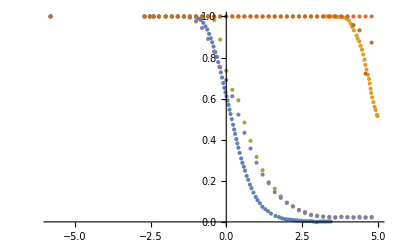

```mathematica
ListPlot[{paperHighT,paperLowT,nhHighT,nhLowT,bdHighT,bdLowT}]
```

```mathematica
nhHighT=Table[{-3+(i-1)*0.2,(Mean/@Transpose[T015nh])[[i]]},{i,1,40}];
nhLowT=Table[{-3+(i-1)*0.2,(Mean/@Transpose[T00055nh])[[i]]},{i,1,40}];
bdHighT = Table[{-3+(i-1)*0.2,(Mean/@Transpose[T015bd])[[i]]},{i,1,40}];
bdLowT = Table[{-3+(i-1)*0.2,(Mean/@Transpose[T00055bd])[[i]]},{i,1,40}];
```

{{-0.164412,0.895954},{-0.13305,0.851638},{-0.106705,0.807322},{-0.0816752,0.766859},{-0.062444,0.73025},{-0.0472084,0.701349},{-0.0317253,0.674374},{-0.0137219,0.643545},{0.00461625,0.603083},{0.0256545,0.570328},{0.0423217,0.537572},{0.069062,0.491329},{0.0914499,0.452794},{0.111743,0.416185},{0.137642,0.377649},{0.166828,0.333333},{0.191263,0.300578},{0.224641,0.262042},{0.256058,0.231214},{0.285319,0.204239},{0.315261,0.177264},{0.3459,0.154143},{0.386801,0.129094},{0.428945,0.1079},{0.468983,0.0905588},{0.506669,0.0751445},{0.563217,0.061657},{0.614436,0.0520231},{0.663497,0.0423892},{0.725932,0.0327553},{0.807281,0.0250482},{0.888111,0.017341},{0.968019,0.0134875},{1.04188,0.00963391},{1.1234,0.00770713},{1.19298,0.00578035},{1.27005,0.00578035},{1.35525,0.00385356},{1.46059,0.00385356},{1.54121,0.00192678},{1.61241,0.00192678},{1.69801,0.00192678},{1.79283,0.00192678},{1.8777,0.00385356},{1.97884,0.00192678},{2.07644,0.00192678},{2.18457,0.00192678},{2.29649,0.00192678},{2.4045,0.00192678},{2.50796,0.00192678},{2.62289,0.00192678},{2.75022,0.00192678}}

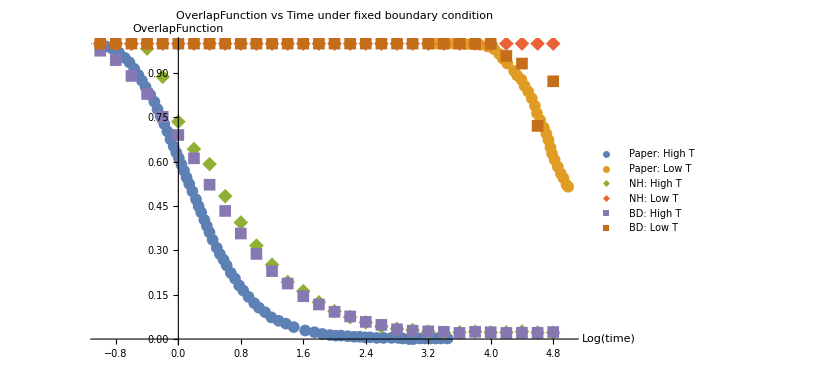

```mathematica
FBQT=ListPlot[{paperHighT,paperLowT,nhHighT,nhLowT,bdHighT,bdLowT},PlotLegends->{"Paper: High T","Paper: Low T", "NH: High T", "NH: Low T", "BD: High T", "BD: Low T"},PlotMarkers->{{"●",12},{"●",12},{"◆",15},{"◆",15},{"■",12},{"■",12}},
PlotLabel->"OverlapFunction vs Time under fixed boundary condition",AxesLabel->{"Log(time)","OverlapFunction"},
PlotRange->{{-1,5},Automatic}]
```

```mathematica
Export["./Learning/Research/G_T/cellGPU/analysescript/overlapvstimeFBC.jpeg",FBQT,ImageSize->8000]
```

./Learning/Research/G_T/cellGPU/analysescript/overlapvstimeFBC.jpeg

```mathematica
#PBD
```

#PBD

```mathematica
FixHighBD=Table[{position,boxMatrix}=readFile["/Users/chengling/Downloads/PBD/bd_N1024_p3.75000_T0.15000000_t100000.000000_",j];
Table[N[computeOverlap[Partition[position[[1]],2],Partition[position[[i]],2],Partition[boxMatrix[[i]],2]]],{i,1,Length[position]}],{j,1,10}];
```

```mathematica
FixHighLow=Table[{position,boxMatrix}=readFile["/Users/chengling/Downloads/PBD/bd_N1024_p3.75000_T0.00055000_t100000.000000_",j];
Table[N[computeOverlap[Partition[position[[1]],2],Partition[position[[i]],2],Partition[boxMatrix[[i]],2]]],{i,1,Length[position]}],{j,1,9}];
```

```mathematica
FixLowNH=Table[{position,boxMatrix}=readFile["/Users/chengling/Downloads/PBD/nvt_N1024_p3.75000_T0.00055000_t100000.000000_",j];
Table[N[computeOverlap[Partition[position[[1]],2],Partition[position[[i]],2],Partition[boxMatrix[[i]],2]]],{i,1,Length[position]}],{j,1,9}];
```

```mathematica
FixHighNH=Table[{position,boxMatrix}=readFile["/Users/chengling/Downloads/PBD/nvt_N1024_p3.75000_T0.15000000_t100000.000000_",j];
Table[N[computeOverlap[Partition[position[[1]],2],Partition[position[[i]],2],Partition[boxMatrix[[i]],2]]],{i,1,Length[position]}],{j,1,9}];
```

```mathematica
PBnhHighT=Table[{Log10[time[[i]]-10000][[1]],(Mean/@Transpose[FixHighBD])[[i]]},{i,1,40}];
PBnhLowT=Table[{Log10[time[[i]]-10000][[1]],(Mean/@Transpose[FixLowNH])[[i]]},{i,1,40}];
PBbdHighT = Table[{Log10[time[[i]]-10000][[1]],(Mean/@Transpose[T015bd])[[i]]},{i,1,40}];
PBbdLowT = Table[{Log10[time[[i]]-10000][[1]],(Mean/@Transpose[FixHighLow])[[i]]},{i,1,40}];
```

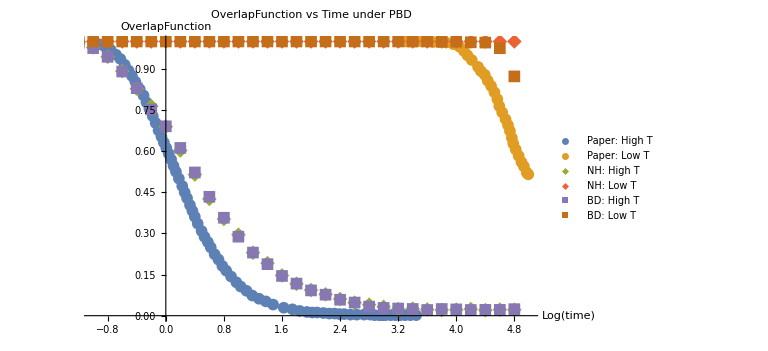

```mathematica
PBQT=ListPlot[{paperHighT,paperLowT,PBnhHighT,PBnhLowT,PBbdHighT,PBbdLowT},PlotLegends->{"Paper: High T","Paper: Low T", "NH: High T", "NH: Low T", "BD: High T", "BD: Low T"},PlotMarkers->{{"●",12},{"●",12},{"◆",15},{"◆",15},{"■",12},{"■",12}},
PlotLabel->"OverlapFunction vs Time under PBD",AxesLabel->{"Log(time)","OverlapFunction"},
PlotRange->{{-1,5},Automatic}]
```

```mathematica
PBnhHighT
```

{{-3.,1.},{-2.8,1.},{-2.6,1.},{-2.4,1.},{-2.2,1.},{-2.,1.},{-1.8,1.},{-1.6,1.},{-1.4,0.99873},{-1.2,0.995117},{-1.,0.978027},{-0.8,0.944141},{-0.6,0.891797},{-0.4,0.827734},{-0.2,0.764258},{0.,0.689258},{0.2,0.602441},{0.4,0.514746},{0.6,0.425684},{0.8,0.352441},{1.,0.295313},{1.2,0.22959},{1.4,0.191504},{1.6,0.146875},{1.8,0.116309},{2.,0.093457},{2.2,0.0779297},{2.4,0.0608398},{2.6,0.0475586},{2.8,0.0401367},{3.,0.0324219},{3.2,0.0238281},{3.4,0.0254883},{3.6,0.0225586},{3.8,0.0207031},{4.,0.0220703},{4.2,0.0242188},{4.4,0.0201172},{4.6,0.0222656},{4.8,0.021582}}

```mathematica
time-1000000
```

{{10000.},{10000.},{10000.},{10000.},{10000.},{10000.},{10000.},{10000.},{10000.},{10000.1},{10000.1},{10000.2},{10000.3},{10000.4},{10000.6},{10001.},{10001.6},{10002.5},{10004.},{10006.3},{10010.},{10015.8},{10025.1},{10039.8},{10063.1},{10100.},{10158.5},{10251.2},{10398.1},{10631.},{11000.},{11584.9},{12511.9},{13981.1},{16309.6},{20000.},{25848.9},{35118.9},{49810.7},{73095.7}}

```mathematica
PBnhHighT[[20,1]]
```

0.800029